```mathematica
CreateDatabin[]
```

Databin[…]

```mathematica
(* For Exporting *)
SetDirectory[NotebookDirectory[]];

bin=Databin["66W7CW2x"];

(* Take the arbitrary number stored and convert it to a DateObject, then a string *)
times=DateObject/@Dataset[bin][All,"Timestamp"]//Normal;

(* Place all data in chronological order *)
chronologicalOrdering=Ordering[times];
latestIndex=chronologicalOrdering[[Length[times]]];
gopDebates=DateObject/@{"August 6, 2015 8pm","September 16, 2015 7pm"};
(* Use the names from the last row to be sure to have them all *)
names=Select[Keys[Dataset[bin][latestIndex]]//Normal,StringContainsQ[#,"("]&];
lastNamesWithParty=Module[{split},(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names];
lastNamesWithoutParty=Module[{split},(split=StringSplit[#];split[[2]])&/@names];

(* Sort names in alpha by last name *)
nameOrdering=Ordering[lastNamesWithParty];
names=names[[nameOrdering]];
lastNamesWithParty=lastNamesWithParty[[nameOrdering]];
lastNamesWithoutParty=lastNamesWithoutParty[[nameOrdering]];

Clear[data];

times=times[[chronologicalOrdering]];
data=names/.(Dataset[bin][chronologicalOrdering,names]//Normal);

(* At this point, all data is in chronological order *)
times=DateString/@times;

dayTimes=N[(AbsoluteTime[#]-AbsoluteTime[times[[Length[times]]]])/(3600*24)]&/@times;

InvalidNum=-1;

data=Module[{emptyData,missingData},
missingData=(MissingQ/@#)&/@(data);
emptyData=
Table[
Table[
If[
Or[
Length[data[[j]]]<i,
missingData[[j,i]]],
InvalidNum,ToExpression[data[[j,i]]]]

,{i,Length[names]}],
{j,Length[data]}]];

firstRecordingDates=Flatten[Position[#,_Integer?(#>0&)]][[1]]&/@Transpose[data];

(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
all = Range[Length[names]];
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Differences[data];

absoluteDiffData=
Table[Table[
If[absoluteDiffData[[r,c]]+InvalidNum==data[[r+1,c]],0,absoluteDiffData[[r,c]]]
,{c,Length[names]}],{r,Length[absoluteDiffData]}];

percentDiffData=absoluteDiffData/data[[1;;Length[data]-1]]//N;

titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};
findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]




graphFn[option_Integer,selection_List,scale_Integer,customStyle_List:{RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998367, 0.434775],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.566842, 0.967407, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.4, 0.8, 1],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.20956699999999995, 0.549706, 0.]},plotRange_:All,highlight_Integer:0]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles,ordering},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData*100]];

(* Sort by choice of graph to make colors better *)
graph=graph[[All,selection]];
labels=labels[[selection]];
ordering=Reverse[Ordering[graph[[Length[graph]]]]];
labels=labels[[ordering]];
graph=graph[[All,ordering]];

graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];
(* Only nicely do the first one, dash the rest. *)
styles=Table[
If[findIndex[labels[[i]]]==highlight,Directive[customStyle[[Mod[i,Length[customStyle],1]]],Thickness[.015]],
If[i<10,customStyle[[Mod[i,Length[customStyle],1]]],Directive[Dashed,customStyle[[Mod[i,Length[customStyle],1]]]]]],
{i,Length[selection]}];


fn[ConvertToTimes[graph,graphTimes],PlotLegends->labels,
PlotLabel->plotLabel,
PlotRange->plotRange,
PlotStyle->styles]]

graphFn[option_Integer,selection_List,OptionsPattern[{Scale->1,CustomStyle->{RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998367, 0.434775],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.566842, 0.967407, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.4, 0.8, 1],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.20956699999999995, 0.549706, 0.]},PlotRange->All,Highlight->0}]]:=graphFn[option,selection,OptionValue[Scale],OptionValue[CustomStyle],OptionValue[PlotRange],OptionValue[Highlight]]

pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]

tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
```

```mathematica
Manipulate[
graphFn[option,selection,Scale->scale,Highlight->highlight],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[Length[names]]},{Range[Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}},
{{highlight,0},Join[{0->"None"},#->names[[#]]&/@Range[Length[names]]]}
]
```

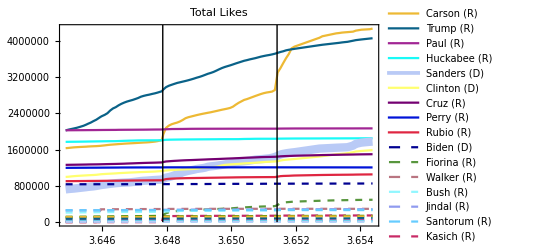

```mathematica
Show[graphFn[1,all,Highlight->findIndex["Sanders"],PlotRange->{{DateObject[times[[1]]],DateObject[times[[Length[times]]]]},All}],Graphics[{Line[{{AbsoluteTime[gopDebates[[1]]],0},{AbsoluteTime[gopDebates[[1]]],5*^6}}],Line[{{AbsoluteTime[gopDebates[[2]]],0},{AbsoluteTime[gopDebates[[2]]],5*^6}}]}]]
```

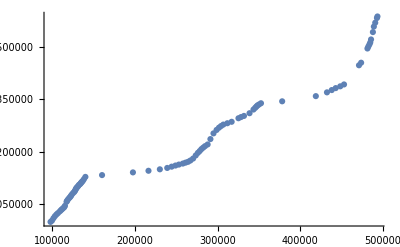

```mathematica
ListPlot[data[[All,{findIndex["Fiorina"],findIndex["Clinton"]}]]]
```

| Joe Biden (D) | Jeb Bush (R) | Ben Carson (R) | Lincoln Chafee (D) | Chris Christie (R) | Hillary Clinton (D) | Ted Cruz (R) | Carly Fiorina (R) | Lindsey Graham (R) | Mike Huckabee (R) | Bobby Jindal (R) | John Kasich (R) | Martin O'Malley (D) | George Pataki (R) | Rand Paul (R) | Rick Perry (R) | Marco Rubio (R) | Bernie Sanders (D) | Rick Santorum (R) | Donald Trump (R) | Scott Walker (R) | Jim Webb (D)
Joe Biden (D) | 1. | 0.00140642 | 0.00267123 | 0.0122688 | 0.0000854014 | 0.393289 | 0.0966859 | 0.0063854 | 0.153823 | 0.00196937 | 0.0233568 | 0.00264674 | 0.0067927 | 0.0143351 | 0.0313853 | 0.195409 | 0.00985542 | 0.103461 | 0.000364072 | 0.206036 | 0.175114 | 0.00978724
Jeb Bush (R) | 0.00140642 | 1. | 0.209116 | 0.00491749 | 0.473103 | 0.0192623 | 0.200354 | 0.315256 | 0.186282 | 0.141721 | 0.226667 | 0.15129 | 0.00608585 | 0.237625 | 0.112878 | 0.0306551 | 0.372101 | 0.171856 | 0.289529 | 0.0653795 | 0.0557622 | 0.00710307
Ben Carson (R) | 0.00267123 | 0.209116 | 1. | 0.00735334 | 0.666192 | 0.0359753 | 0.302779 | 0.397546 | 0.537212 | 0.274247 | 0.485299 | 0.315357 | 0.00948653 | 0.775757 | 0.152729 | 0.0159626 | 0.560056 | 0.186957 | 0.656485 | 0.152432 | 0.0421599 | 0.0143337
Lincoln Chafee (D) | 0.0122688 | 0.00491749 | 0.00735334 | 1. | 0.00244387 | 0.0945712 | 0.00154518 | 0.0064057 | 0.0346556 | 0.00440538 | 0.00454165 | 0.00234031 | 0.895907 | 0.0010136 | 0.00482403 | 0.118382 | 0.0000255869 | 0.0829723 | 0.00756625 | 0.0015346 | 0.0392904 | 0.878371
Chris Christie (R) | 0.0000854014 | 0.473103 | 0.666192 | 0.00244387 | 1. | 0.0407778 | 0.291462 | 0.588256 | 0.455331 | 0.231272 | 0.469514 | 0.367618 | 0.0039339 | 0.649473 | 0.243611 | 0.0294695 | 0.749871 | 0.18384 | 0.638946 | 0.0967522 | 0.0612339 | 0.00528952
Hillary Clinton (D) | 0.393289 | 0.0192623 | 0.0359753 | 0.0945712 | 0.0407778 | 1. | 0.323631 | 0.0117284 | 0.348093 | 0.0258273 | 0.0417088 | 0.0103564 | 0.0701474 | 0.026147 | 0.000677705 | 0.353609 | 0.144663 | 0.279877 | 0.0278736 | 0.382673 | 0.316179 | 0.0540309
Ted Cruz (R) | 0.0966859 | 0.200354 | 0.302779 | 0.00154518 | 0.291462 | 0.323631 | 1. | 0.551487 | 0.345944 | 0.627499 | 0.626489 | 0.545835 | 0.00888693 | 0.197618 | 0.297739 | 0.0274106 | 0.655754 | 0.551654 | 0.35092 | 0.797172 | 0.0187856 | 0.01515
Carly Fiorina (R) | 0.0063854 | 0.315256 | 0.397546 | 0.0064057 | 0.588256 | 0.0117284 | 0.551487 | 1. | 0.156674 | 0.638705 | 0.759524 | 0.906997 | 0.0102579 | 0.335467 | 0.624232 | 0.336172 | 0.83938 | 0.250558 | 0.507289 | 0.323736 | 0.341604 | 0.0114108
Lindsey Graham (R) | 0.153823 | 0.186282 | 0.537212 | 0.0346556 | 0.455331 | 0.348093 | 0.345944 | 0.156674 | 1. | 0.13416 | 0.295985 | 0.0805275 | 0.0148572 | 0.581351 | 0.0388062 | 0.0966314 | 0.379275 | 0.308548 | 0.435688 | 0.282801 | 0.0304126 | 0.0148232
Mike Huckabee (R) | 0.00196937 | 0.141721 | 0.274247 | 0.00440538 | 0.231272 | 0.0258273 | 0.627499 | 0.638705 | 0.13416 | 1. | 0.549601 | 0.628378 | 0.00654997 | 0.149457 | 0.296338 | 0.213032 | 0.48553 | 0.199681 | 0.285093 | 0.424076 | 0.236385 | 0.00875961
Bobby Jindal (R) | 0.0233568 | 0.226667 | 0.485299 | 0.00454165 | 0.469514 | 0.0417088 | 0.626489 | 0.759524 | 0.295985 | 0.549601 | 1. | 0.727429 | 0.0131024 | 0.451582 | 0.471816 | 0.21563 | 0.721672 | 0.352176 | 0.56868 | 0.535127 | 0.210712 | 0.0193108
John Kasich (R) | 0.00264674 | 0.15129 | 0.315357 | 0.00234031 | 0.367618 | 0.0103564 | 0.545835 | 0.906997 | 0.0805275 | 0.628378 | 0.727429 | 1. | 0.00511329 | 0.228967 | 0.573446 | 0.375985 | 0.727684 | 0.277057 | 0.397446 | 0.36916 | 0.32537 | 0.00507941
Martin O'Malley (D) | 0.0067927 | 0.00608585 | 0.00948653 | 0.895907 | 0.0039339 | 0.0701474 | 0.00888693 | 0.0102579 | 0.0148572 | 0.00654997 | 0.0131024 | 0.00511329 | 1. | 0.00399706 | 0.00719752 | 0.109011 | 0.00104967 | 0.0755708 | 0.0143273 | 0.000759821 | 0.0320632 | 0.955076
George Pataki (R) | 0.0143351 | 0.237625 | 0.775757 | 0.0010136 | 0.649473 | 0.026147 | 0.197618 | 0.335467 | 0.581351 | 0.149457 | 0.451582 | 0.228967 | 0.00399706 | 1. | 0.17793 | 0.0101426 | 0.47101 | 0.213166 | 0.707567 | 0.107812 | 0.0483661 | 0.00548717
Rand Paul (R) | 0.0313853 | 0.112878 | 0.152729 | 0.00482403 | 0.243611 | 0.000677705 | 0.297739 | 0.624232 | 0.0388062 | 0.296338 | 0.471816 | 0.573446 | 0.00719752 | 0.17793 | 1. | 0.250381 | 0.489705 | 0.169871 | 0.366565 | 0.165632 | 0.301999 | 0.00583169
Rick Perry (R) | 0.195409 | 0.0306551 | 0.0159626 | 0.118382 | 0.0294695 | 0.353609 | 0.0274106 | 0.336172 | 0.0966314 | 0.213032 | 0.21563 | 0.375985 | 0.109011 | 0.0101426 | 0.250381 | 1. | 0.0690178 | 0.00189062 | 0.0609595 | 0.0134099 | 0.763045 | 0.118262
Marco Rubio (R) | 0.00985542 | 0.372101 | 0.560056 | 0.0000255869 | 0.749871 | 0.144663 | 0.655754 | 0.83938 | 0.379275 | 0.48553 | 0.721672 | 0.727684 | 0.00104967 | 0.47101 | 0.489705 | 0.0690178 | 1. | 0.420984 | 0.62106 | 0.38027 | 0.0681358 | 0.00130681
Bernie Sanders (D) | 0.103461 | 0.171856 | 0.186957 | 0.0829723 | 0.18384 | 0.279877 | 0.551654 | 0.250558 | 0.308548 | 0.199681 | 0.352176 | 0.277057 | 0.0755708 | 0.213166 | 0.169871 | 0.00189062 | 0.420984 | 1. | 0.276193 | 0.465419 | 0.00050463 | 0.0666231
Rick Santorum (R) | 0.000364072 | 0.289529 | 0.656485 | 0.00756625 | 0.638946 | 0.0278736 | 0.35092 | 0.507289 | 0.435688 | 0.285093 | 0.56868 | 0.397446 | 0.0143273 | 0.707567 | 0.366565 | 0.0609595 | 0.62106 | 0.276193 | 1. | 0.19888 | 0.0950308 | 0.015462
Donald Trump (R) | 0.206036 | 0.0653795 | 0.152432 | 0.0015346 | 0.0967522 | 0.382673 | 0.797172 | 0.323736 | 0.282801 | 0.424076 | 0.535127 | 0.36916 | 0.000759821 | 0.107812 | 0.165632 | 0.0134099 | 0.38027 | 0.465419 | 0.19888 | 1. | 0.00568625 | 0.00466317
Scott Walker (R) | 0.175114 | 0.0557622 | 0.0421599 | 0.0392904 | 0.0612339 | 0.316179 | 0.0187856 | 0.341604 | 0.0304126 | 0.236385 | 0.210712 | 0.32537 | 0.0320632 | 0.0483661 | 0.301999 | 0.763045 | 0.0681358 | 0.00050463 | 0.0950308 | 0.00568625 | 1. | 0.0370244
Jim Webb (D) | 0.00978724 | 0.00710307 | 0.0143337 | 0.878371 | 0.00528952 | 0.0540309 | 0.01515 | 0.0114108 | 0.0148232 | 0.00875961 | 0.0193108 | 0.00507941 | 0.955076 | 0.00548717 | 0.00583169 | 0.118262 | 0.00130681 | 0.0666231 | 0.015462 | 0.00466317 | 0.0370244 | 1.

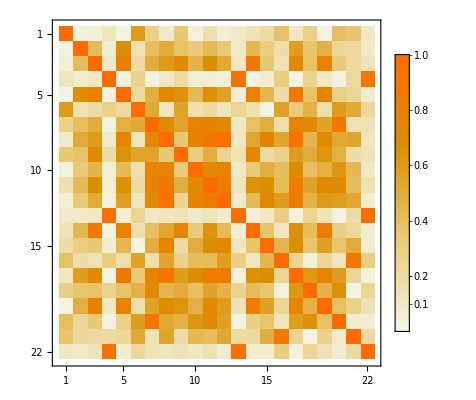

```mathematica
rsquared=Table[Table[LinearModelFit[percentDiffData[[Max[firstRecordingDates];;,{i,j}]],x,x]["RSquared"]&[i,j],{j,Length[names]}],{i,Length[names]}];
TableForm[rsquared,TableHeadings->{names,names}]
MatrixPlot[rsquared,PlotLegends->Automatic]
```

```mathematica
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,Length[times],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
CloudDeploy[%269,Permissions->"Public"]
```

CloudObject[]

```mathematica
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
Export["table.png",tableFn[1,1,Length[times]-1,Range[Length[names]]],ImageResolution->500]
```

table.png

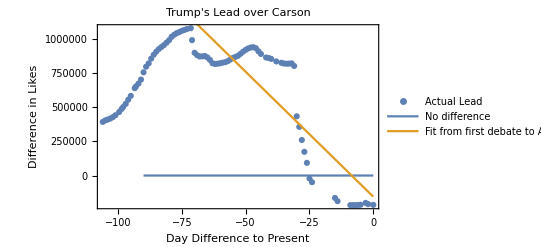

```mathematica
Show[ListPlot[{dayTimes,data[[All,findIndex["Trump"]]]-data[[All,findIndex["Carson"]]]}//Transpose,
PlotLegends->{"Actual Lead"}],
Plot[{0,
Normal[LinearModelFit[{dayTimes[[35;;-4]],data[[35;;-4,findIndex["Trump"]]]-data[[35;;-4,findIndex["Carson"]]]}//Transpose,{x},x]]/.{x->t}},{t,-Length[data],0},
PlotLegends->{"No difference","Fit from first\ndebate to \nAugust 19"}],
PlotLabel->"Trump's Lead over Carson",
FrameLabel->{"Day Difference to Present","Difference in Likes"},
Frame->True
]
```

```mathematica
LinearModelFit[{dayTimes[[35;;#]]-dayTimes[[35]],data[[35;;#,findIndex["Clinton"]]]-data[[35;;#,findIndex["Sanders"]]]}//Transpose,{x},x]["AdjustedRSquared"]&/@Range[37,Length[data]]
```

{0.970448,0.911148,0.943355,0.971373,0.983417,0.989498,0.985443,0.988817,0.991758,0.992933,0.992074,0.990442,0.982903,0.971353,0.962089,0.959835,0.956401,0.950856,0.944284,0.92974,0.908073,0.886971,0.869972,0.857503,0.848539,0.847702,0.849059,0.846283,0.84498,0.845293,0.84851,0.847261,0.845477,0.844779,0.844688,0.8481,0.854899,0.864416,0.874192,0.882681,0.89031,0.897074,0.902993,0.908043,0.91138,0.912763,0.89945,0.887588,0.876461,0.865803,0.854613,0.848128,0.849571,0.85359}

```mathematica
(*Some options...

dayToStart=times[[1]];
dayToStart=times[[Max[firstRecordingDates]]];
dayToStart=gopDebates[[1]];
dayToStart=gopDebates[[2]];

*)
dayToStart=gopDebates[[1]];
dataStart=Flatten[Position[(DateObject[#]≥DateObject[dayToStart])&/@times,True]][[1]];
Manipulate[
Quiet[Quiet[
Labeled[TableForm[Sort[{lastNamesWithParty[[#]],(LinearModelFit[({dayTimes[[dataStart;;]],data[[dataStart;;,#]]}//Transpose),{x},x]["BestFit"]/.{x->time})}&/@(findIndex/@lastNamesWithoutParty),#1[[2]]>#2[[2]]&]],
"Estimated Total Likes from Linear Fit\n"<>DatePlus[times[[Length[times]]],time]
,Top]],{Part::pkspec1}],{time,1,QuantityMagnitude[DateDifference[Today,DateObject[{2016,11,8}]]],1}]
```

```mathematica
(*
(* VERY OLD CODE *)
SetDirectory[NotebookDirectory[]];
data2=Import["like_data.csv"];
bin=Databin["66W7CW2x"];
names=data2[[1]];
data2=data2[[2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data2[[j]]]<i,
StringLength[ToString[data2[[j,i]]]]==0],
InvalidNum,data2[[j,i]]]

,{i,Length[names]}],{j,Length[data2]}];
data2=emptyData;

(* Add literally everything *)
For[i=1,i≤Length[data2],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[i,1;;Length[names]]]}]]]]
(*  THIS IS THE IMPORTANT ONE -- HOW TO ADD IN CASE OF ERROR   *)
data2=Import["like_data.csv"];
names=data2[[1]];
DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[Length[data2],1;;Length[names]]]}]]]


times=(DateObject/@Dataset[bin][All,"Timestamp"]);*)
(*ResetTheDatabin[]:=For[i=0,i<Length[data],i++,DatabinRemove[bin,1]]*)
(*For[i=1,i≤Length[data],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data[[i]]}]]]]*)
```

```mathematica
RandomSample[Flatten[{#,ColorNegate[#]}&/@Flatten[MapThread[{#1,#2}&,{(*Table[ColorData["VisibleSpectrum"][410+(i/22)^1*(720-410)],{i,1,21,1}],*)ColorData[60,"ColorList"],ColorData[54,"ColorList"]}]]],22]
```

{RGBColor[0.21719699999999997, 0.8350960000000001, 0.599542],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.501961, 0, 0.25098],RGBColor[0.24078699999999997, 0.11311499999999997, 0.680735],RGBColor[0.6, 0.19999999999999996, 0.],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.511666, 0.141085],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0.36990900000000004, 0.851804, 0.420539],RGBColor[0., 0., 0.607843],RGBColor[0.85037, 0.558389, 0],RGBColor[1, 0.740871, 0.828473],RGBColor[0.829938, 0.725154, 1],RGBColor[0., 0.6, 0.6],RGBColor[1, 0.529198, 0.324819],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0., 0.19999999999999996, 0.6],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[1, 0.998856, 0.00207523],RGBColor[0.131228, 0.26041000000000003, 0.781384],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.43315800000000004, 0.03259299999999998, 0.]}

```mathematica
Module[{m},m=Sort[{#,100(data[[Length[data],findIndex[#]]]/data[[firstRecordingDates[[findIndex[#]]],findIndex[#]]]-1)//N,data[[Length[data],findIndex[#]]]}&/@lastNamesWithParty,#1[[2]]>#2[[2]]&];
Labeled[TableForm[{"+"<>ToString[#[[1]]]<>"%",#[[2]]}&/@m[[All,{2,3}]],TableHeadings->{m[[All,1]],{"Percent Change","Total Likes"}}],"Percent change since July 3\nOr first date on record [Kasich, Walker]",Top]]
```

| Percent Change | Total Likes
Fiorina (R) | +383.589% | 473733
Carson (R) | +151.308% | 4100594
Sanders (D) | +125.077% | 1625761
Trump (R) | +93.3608% | 3913215
Clinton (D) | +45.8025% | 1454934
Bush (R) | +34.7369% | 283384
Webb (D) | +30.0234% | 31649
Chafee (D) | +22.781% | 9766
Pataki (R) | +18.011% | 19093
Kasich (R) | +17.8687% | 146433
Cruz (R) | +17.1093% | 1479625
Graham (R) | +15.371% | 136402
Rubio (R) | +15.148% | 1040385
Christie (R) | +14.3961% | 125949
O'Malley (D) | +9.97926% | 80055
Jindal (R) | +9.80156% | 284027
Huckabee (R) | +4.30341% | 1847011
Walker (R) | +3.91585% | 293953
Paul (R) | +1.99481% | 2066828
Biden (D) | +1.71246% | 849893
Santorum (R) | +1.02844% | 265431
Perry (R) | +0.876534% | 1208170Percent change since July 3
Or first date on record [Kasich, Walker]

```mathematica
(*(* Probably one-time code to fix Scott Walker. I originally copied in the first value recorded, but this made things kinda messy. Instead, I'm going to store -1. *)
newbin=bin;
(* Set "constant placeholders" to -1 *)
linesToUpdate=Flatten[Position[DateObject[#]<DateObject["15 Jul 2015 13:13:00"]&/@times,True]];
data[[linesToUpdate,findIndex["Walker"]]]=InvalidNum;
(* Try adding new rows to a Databin INCLUDING timestamp *)
DatabinAdd[newbin,Association[Join[MapThread[#1->#2&,{names,data[[#]]}],{"Timestamp"->times[[#]]}]]]&/@linesToUpdate;
(* Delete old rows *)
For[i=1,i≤Length[linesToUpdate],i++,DatabinRemove[newbin,Sort[linesToUpdate,Greater][[i]]]]
*)
```

```mathematica
leadFn[one_String,two_String,time_]:=Show[ListPlot[{dayTimes,data[[All,findIndex[one]]]-data[[All,findIndex[two]]]}//Transpose,
PlotLegends->{"Actual Lead"}],
Plot[{0,
Normal[LinearModelFit[{dayTimes[[time;;]],data[[time;;,findIndex[one]]]-data[[time;;,findIndex[two]]]}//Transpose,{x},x]]/.{x->t}},{t,dayTimes[[time]],0},
PlotLegends->{"No difference","Fit from first\ndebate to \nPresent"}],
PlotLabel->one<>"'s Lead over "<>two,
FrameLabel->{"Day Difference to Present","Difference in Likes"},
Frame->True
]
```

```mathematica
Manipulate[leadFn[one,two,t],{{one,"Carson"},lastNamesWithoutParty},{{two,"Trump"},lastNamesWithoutParty},{t,1,Length[dayTimes],1}]
```

```mathematica
getLikeCountForURL[url_String]:=Import["http://graph.facebook.com/fql?q=select%20%20like_count%20from%20link_stat%20where%20url=%22"<>url<>"%22","JSON"][[1,2,1,1,2]]
candidates=Get["candidates.m"];
getLikeCountForAllCandidates[]:=getLikeCountForURL/@candidates
task=ScheduledTask[
DatabinAdd[bin,getLikeCountForAllCandidates[]]&,{DatePlus[Now,Quantity[1,"minute"]]},
NotificationFunction->(SendMail["To"->$WolframID,
"Subject"->"Test",
"Body"->"Something happened"
]&)];
```

```mathematica
With[{shortid="66W7CW2x",candidates=<|"Joe Biden (D)"->"http://www.facebook.com/joebiden","Lincoln Chafee (D)"->"http://www.facebook.com/chafee2016","Hillary Clinton (D)"->"http://www.facebook.com/hillaryclinton","Martin O'Malley (D)"->"http://www.facebook.com/MartinOMalley","Bernie Sanders (D)"->"http://www.facebook.com/berniesanders","Jim Webb (D)"->"http://www.facebook.com/IHeardMyCountryCalling","Jeb Bush (R)"->"http://www.facebook.com/jebbush","Ben Carson (R)"->"http://www.facebook.com/realbencarson","Chris Christie (R)"->"http://www.facebook.com/govchristie","Ted Cruz (R)"->"http://www.facebook.com/tedcruzpage","Carly Fiorina (R)"->"http://www.facebook.com/CarlyFiorina","Lindsey Graham (R)"->"http://www.facebook.com/LindseyGrahamSC","Mike Huckabee (R)"->"http://www.facebook.com/mikehuckabee","Bobby Jindal (R)"->"http://www.facebook.com/bobbyjindal","George Pataki (R)"->"http://www.facebook.com/GovGeorgePataki","Rand Paul (R)"->"http://www.facebook.com/RandPaul","Rick Perry (R)"->"http://www.facebook.com/GovernorPerry","Marco Rubio (R)"->"http://www.facebook.com/MarcoRubio","Rick Santorum (R)"->"http://www.facebook.com/RickSantorum","Donald Trump (R)"->"http://www.facebook.com/DonaldTrump","Scott Walker (R)"->"http://www.facebook.com/governorscottwalker","John Kasich (R)"->"http://www.facebook.com/JohnKasich"|>},
CloudDeploy[ScheduledTask[
Print["Hey, I got here..."];
getLikeCountForURL[url_String]:=Module[{},
Import["http://graph.facebook.com/fql?q=select%20%20like_count%20from%20link_stat%20where%20url=%22"<>url<>"%22","JSON"][[1,2,1,1,2]]];
getLikeCountForAllCandidates[]:=Module[{},getLikeCountForURL/@candidates];
Print["I defined my functions...."];
val=getLikeCountForAllCandidates[];
Print[val];
bin=Databin[shortid];
Print["bin created"];
 DatabinAdd[bin,val];
Print["Added to bin"];
,DateObject[{_,_,_,12,00}]],"FB Election 1"]
]
```

CloudObject[]